```mathematica
Plot of Br(r,z) and Bz(z) in the case of nonlinear solenoid
```

```mathematica
ClearAll[R,l,Lz,Br,Bz,r,z,θ,GNR,GNZ];
R=0.08;(*Radius of coil*)
l=0.3;(*Length of coil*)
Bz00[r_,z_]:=NIntegrate[1/(2π)((R^2-R*r*Cos[θ])/(R^2+r^2-2R*r*Cos[θ]))*((z+l/2)/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(z-l/2)/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ]))),{θ,0,2π}]

Bz0=Bz00[0,0];(*Scaling factor of magnetic fields*)
Br[r_,z_]:=NIntegrate[1/(2π)*((R*Cos[θ])/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(R*Cos[θ])/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))),{θ,0,2π}]/Bz0;(*Scaled Br field*)
Bz[r_,z_]:=NIntegrate[1/(2π)((R^2-R*r*Cos[θ])/(R^2+r^2-2R*r*Cos[θ]))*((z+l/2)/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(z-l/2)/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ]))),{θ,0,2π}]/Bz0;(*Scaled Bz field*)
```

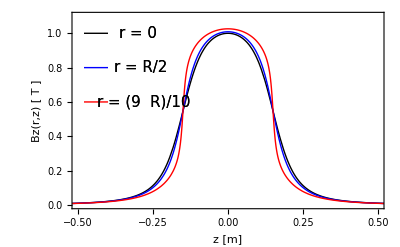

```mathematica
GList[1]={{{-0.3,1}},{{-0.29,0.8}},{{-0.28,0.6}}};

Bzfield[1]=Show[
Plot[Bz[0,z],{z,-1,1},PlotStyle->{Black},Frame->True,PlotRange->{{-0.5,0.5},{0,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z [m]","Bz(r,z) [ T ]"}],
Plot[Bz[0.04,z],{z,-1,1},PlotStyle->{Blue},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}],
Plot[Bz[0.072,z],{z,-1,1},PlotStyle->{Red},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}],

ListPlot[GList[1],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"r = 0",15},{"r = R/2",15},{"r = (9  R)/10",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{-0.48,1},{-0.4,1}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black}],
ListPlot[{{-0.48,0.8},{-0.4,0.8}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Blue}],
ListPlot[{{-0.48,0.6},{-0.4,0.6}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Red}]
]
```

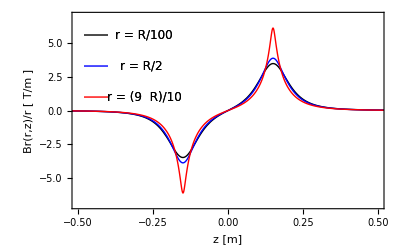

```mathematica
GList[2]={{{-0.28,5.6}},{{-0.29,3.3}},{{-0.28,1.0}}};

Brfield[1]=Show[
Plot[Br[0.0008,z]/0.0008,{z,-1,1},PlotStyle->{Black},Frame->True,PlotRange->{{-0.5,0.5},{-7,7}},Axes->None,LabelStyle->Directive[15],FrameLabel->{"z [m]","Br(r,z)/r [ T/m ]"}],
Plot[Br[0.04,z]/0.04,{z,-1,1},PlotStyle->{Blue},Frame->True,PlotRange->{{-0.5,0.5},{-10,10}},Axes->None,LabelStyle->Directive[15],FrameLabel->{"z_coordinate[m]","Scaled Bz"}],
Plot[Br[0.072,z]/0.072,{z,-1,1},PlotStyle->{Red},Frame->True,PlotRange->{{-0.5,0.5},{-10,10}},Axes->None,LabelStyle->Directive[15],FrameLabel->{"z_coordinate[m]","Scaled Bz"}],

ListPlot[GList[2],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"r = R/100",12},{"r = R/2",12},{"r = (9  R)/10",12}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{-0.48,5.6},{-0.4,5.6}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black}],
ListPlot[{{-0.48,3.3},{-0.4,3.3}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Blue}],
ListPlot[{{-0.48,1},{-0.4,1}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Red}]
]
```

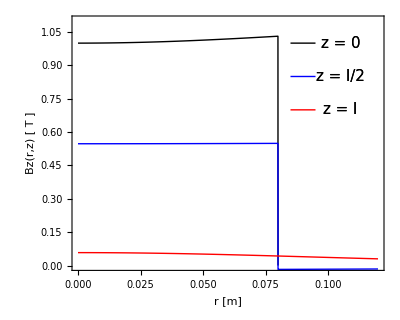

```mathematica
GList[3]={{{0.105,1}},{{0.105,0.85}},{{0.105,0.70}}};

Bzfield[2]=Show[
Plot[Bz[r,0],{r,0,0.12},PlotStyle->{Black},Frame->True,PlotRange->{{0,0.12},{0,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"r [m]","Bz(r,z) [ T ]"},AspectRatio->0.8],
Plot[Bz[r,0.15],{r,0,0.12},PlotStyle->{Blue},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}],
Plot[Bz[r,0.3],{r,0,0.12},PlotStyle->{Red},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}],

ListPlot[GList[3],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"z = 0",15},{"z = l/2",15},{"z = l",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{0.085,1},{0.095,1}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black}],
ListPlot[{{0.085,0.85},{0.095,0.85}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Blue}],
ListPlot[{{0.085,0.7},{0.095,0.7}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Red}]
]
```

```mathematica
Plot of Br(r,z) and Bz(z) in the case of linear solenoid
```

```mathematica
B[z_]:=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));

Bz[r_,z_]:=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/B[0];
Br[r_,z_]:=-0.5*r*(-1/(√(0.01+(-0.25+z)^2))+(-0.25+z)^2/((0.01+(-0.25+z)^2)^(3/2))-(0.25+z)^2/((0.01+(0.25+z)^2)^(3/2))+1/(√(0.01+(0.25+z)^2)))/B[0];
```

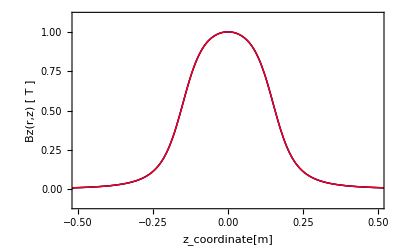

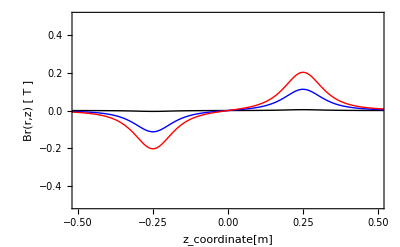

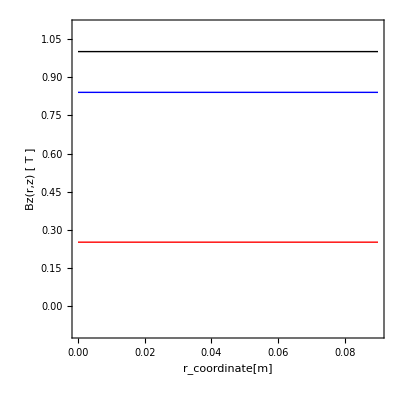

```mathematica
Bzfield[1]=Show[
Plot[Bz[0,z],{z,-1,1},PlotStyle->{Black},Frame->True,PlotRange->{{-0.5,0.5},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Bz(r,z) [ T ]"}],
Plot[Bz[0,z],{z,-1,1},PlotStyle->{Blue},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}],
Plot[Bz[0,z],{z,-1,1},PlotStyle->{Red},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}]
]
Brfield[1]=Show[
Plot[Br[0.08*0.02,z],{z,-1,1},PlotStyle->{Black},Frame->True,PlotRange->{{-0.5,0.5},{-0.5,0.5}},Axes->None,LabelStyle->Directive[15],FrameLabel->{"z_coordinate[m]","Br(r,z) [ T ]"}],
Plot[Br[0.04,z],{z,-1,1},PlotStyle->{Blue},Frame->True,PlotRange->{{-2,2},{-0.5,1.1}},Axes->None,LabelStyle->Directive[15],FrameLabel->{"z_coordinate[m]","Scaled Bz"}],
Plot[Br[0.072,z],{z,-1,1},PlotStyle->{Red},Frame->True,PlotRange->{{-2,2},{-0.5,1.1}},Axes->None,LabelStyle->Directive[15],FrameLabel->{"z_coordinate[m]","Scaled Bz"}]
]
Bzfield[2]=Show[
Plot[Bz[r,0],{r,0,0.09},PlotStyle->{Black},Frame->True,PlotRange->{{0,0.09},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"r_coordinate[m]","Bz(r,z) [ T ]"},AspectRatio->1],
Plot[Bz[r,0.1],{r,0,0.09},PlotStyle->{Blue},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}],
Plot[Bz[r,0.2],{r,0,0.09},PlotStyle->{Red},Frame->True,PlotRange->{{-2,2},{-0.1,1.1}},LabelStyle->Directive[15],Axes->None,FrameLabel->{"z_coordinate[m]","Scaled Bz"}]
]
```